# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["/Users/pcs/Desktop/Quantum channel/Old/Open Ising positive sector/QMB_offline copy.wl"]
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
Clear[haar];
haar[dim_Integer]:=Module[{l=2^dim,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
(*Define the Pauli matrices*)
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
(*Define collective spin operators for n spins*)
Clear[Jx,Jy,Jz];
Jx[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sx,IdentityMatrix[2]],{j,n}],{i,n}];
Jy[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sy,IdentityMatrix[2]],{j,n}],{i,n}];
Jz[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,n}],{i,n}];
(*Define the Lipkin Hamiltonian*)
Clear[Hlmg];
Hlmg[α_,gx_,gy_,n_]:=α*Jz[n]+(gx/(n-1))(Jx[n].Jx[n])+(gy/(n-1))(Jy[n].Jy[n]);

Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Chop[Total[Map[VNentropy,Chop[Eigenvalues[rho]]]]]
];
(*Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];*)
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Tr[Chop[rho.rho]]
];
(*Define subsystem dimensions*)
(*Compute the Page value using the digamma function*)
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
```

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

# Ising scatter plots

```mathematica
L=8;
hx=1;
J=1;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
La=1;
Lb=L-La;
sdiageigenvec=ParallelTable[sdiag[L,La,Lb,i],{i,eigenvec},DistributedContexts->Full];
```

```mathematica
Mean[sdiageigenvec]
```

0.634243

```mathematica
Mean[sdiageigenvec]
```

0.370644

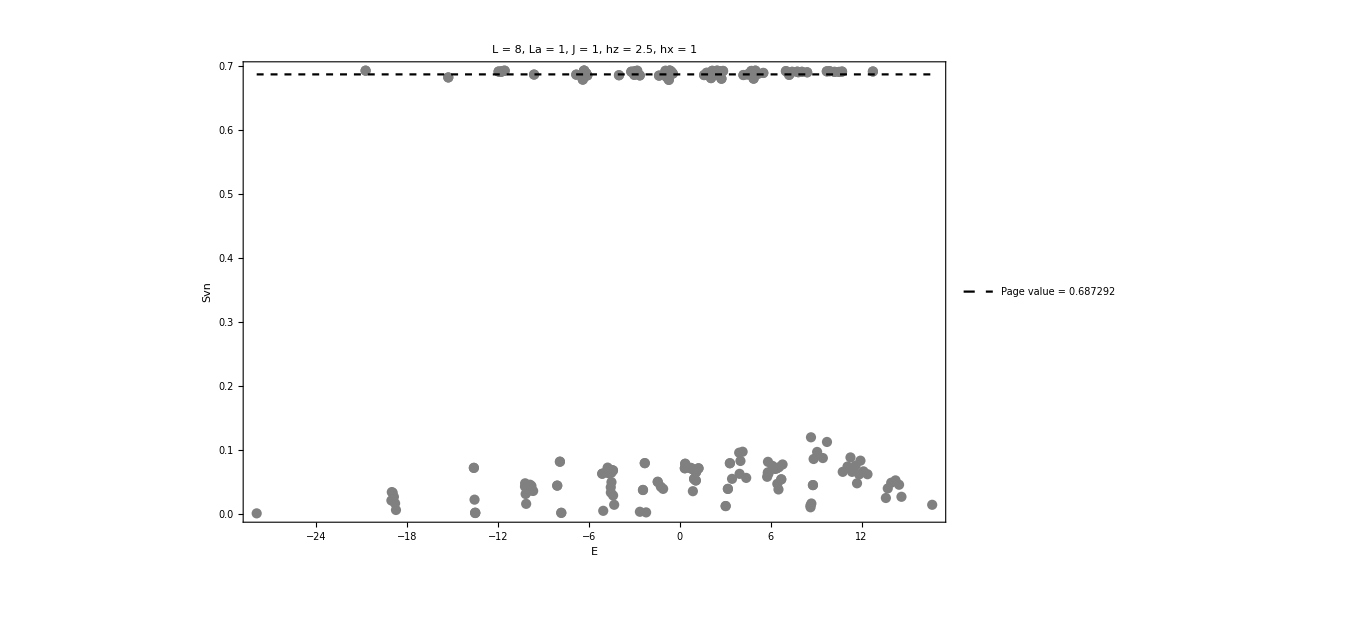

```mathematica
Show[{ListPlot[Transpose[{eigenval,sdiageigenvec}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", hx = "<>ToString[hx],30,Black],PlotStyle->{Directive[Gray,Opacity[1]]},PlotRange->All,ImageSize->1000,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["Svn"]}],Plot[pageEntropy[La,Lb],{x,Min[eigenval],Max[eigenval]},PlotStyle->{Directive[Black,Dashed]},PlotLegends->{Style["Page value = "<>ToString[N[pageEntropy[La,Lb]]],20,Black]}]},PlotRange->All]
```

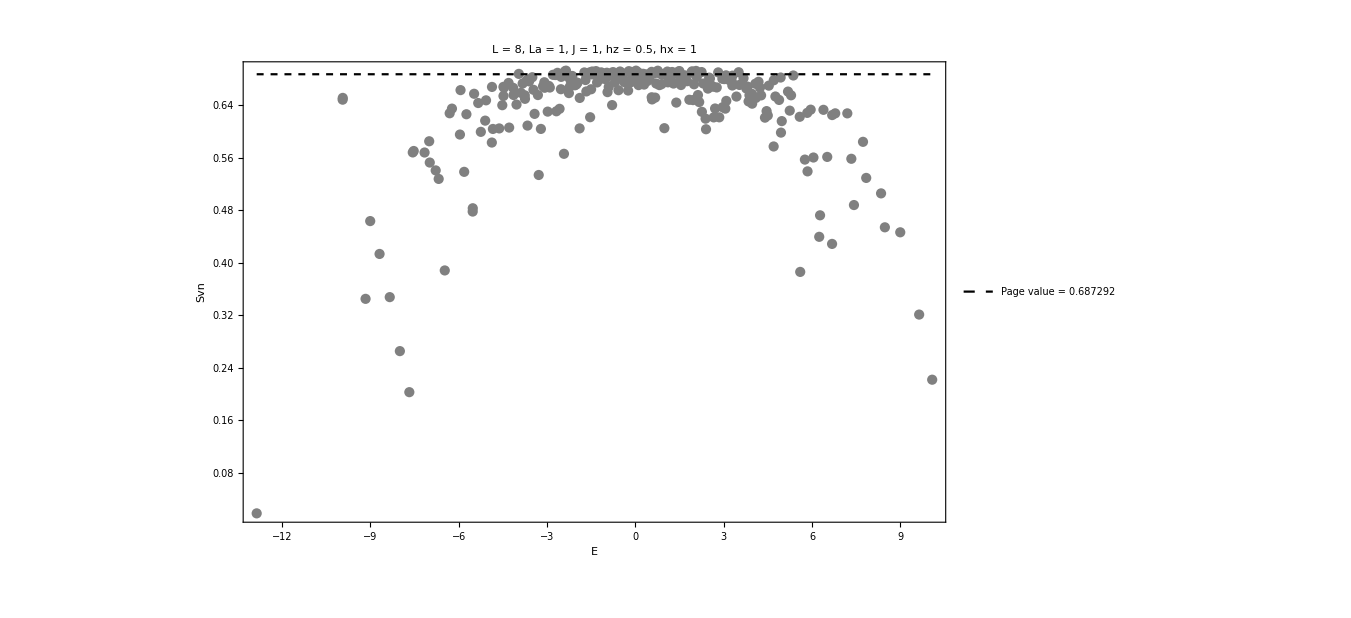

```mathematica
Show[{ListPlot[Transpose[{eigenval,sdiageigenvec}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", hx = "<>ToString[hx],30,Black],PlotStyle->{Directive[Gray,Opacity[1]]},PlotRange->All,ImageSize->1000,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["Svn"]}],Plot[pageEntropy[La,Lb],{x,Min[eigenval],Max[eigenval]},PlotStyle->{Directive[Black,Dashed]},PlotLegends->{Style["Page value = "<>ToString[N[pageEntropy[La,Lb]]],20,Black]}]},PlotRange->All]
```

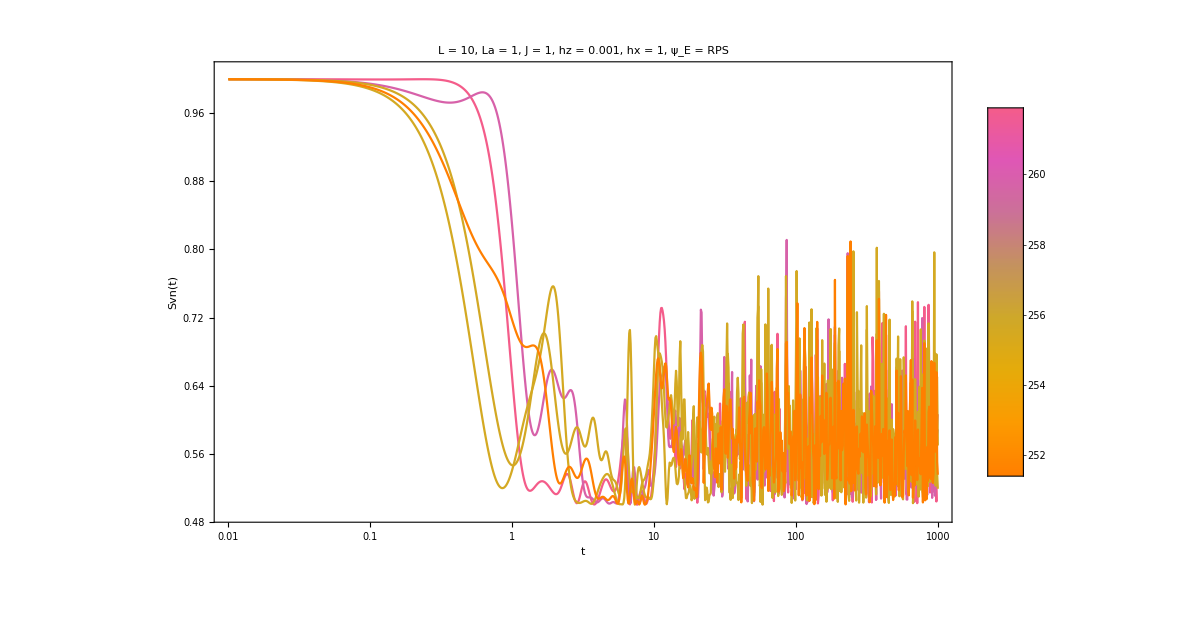

```mathematica
sorted=1/data[[All,1]];
{Emin,Emax}={Min[sorted],Max[sorted]};
colorMapping[e_]:=ColorData["FruitPunchColors"][Rescale[e,{Emin,Emax}]];
(*plot*)
plots=Table[ListLogLinearPlot[svnt[[i]],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", hx = "<>ToString[hx]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->{{tlist[[-1]],tlist[[1]]},{0.49,1.01}},ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]]]],{i,Length[productstate]}];
Legended[Show[{plots}],BarLegend[{"FruitPunchColors",{Emin,Emax}},LabelStyle->{FontSize->12}]]
```

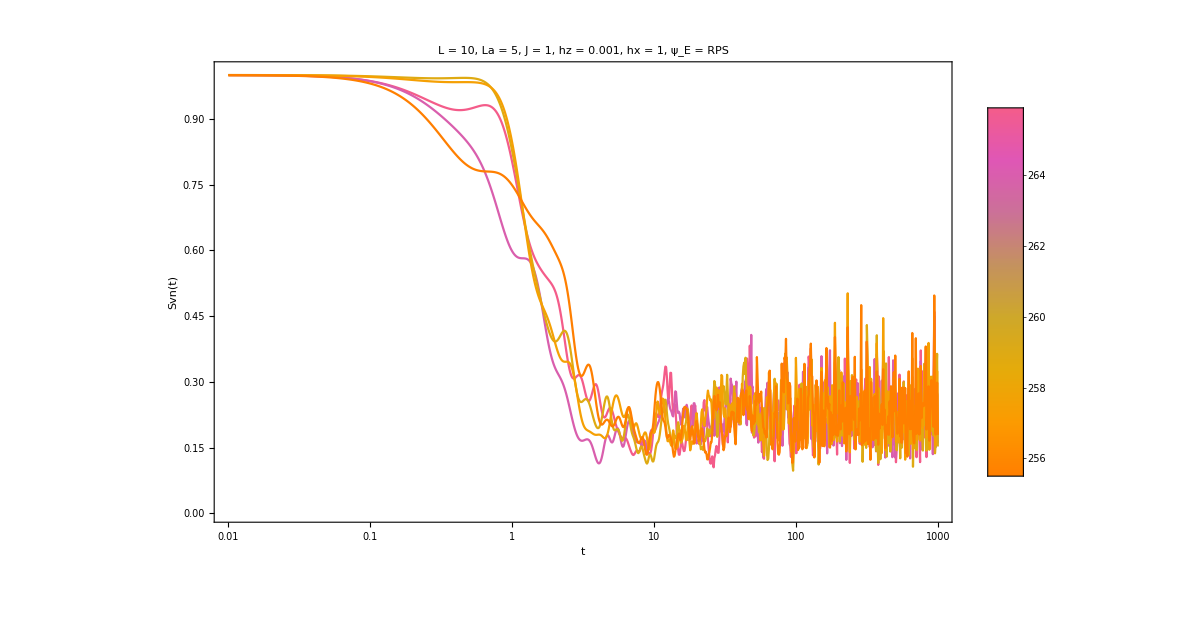

```mathematica
sorted=1/data[[All,1]];
{Emin,Emax}={Min[sorted],Max[sorted]};
colorMapping[e_]:=ColorData["FruitPunchColors"][Rescale[e,{Emin,Emax}]];
(*plot*)
plots=Table[ListLogLinearPlot[svnt[[i]],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", hx = "<>ToString[hx]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->{{tlist[[-1]],tlist[[1]]},{0,1.01}},ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]]]],{i,Length[productstate]}];
Legended[Show[{plots}],BarLegend[{"FruitPunchColors",{Emin,Emax}},LabelStyle->{FontSize->12}]]
```

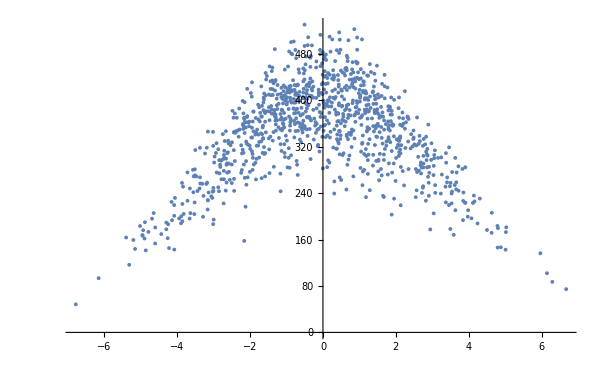

```mathematica
productstate2=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[eigenvec].i]^4]],{i,productstate2},DistributedContexts->Full];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstate2},DistributedContexts->Full];
ListPlot[Transpose[{energies,1/iprs}],PlotRange->All,ImageSize->600]
```

```mathematica
data=SortBy[Transpose[{1/iprs,energies,productstate2}],First];
productstate=data[[1;;-1;;200]][[All,3]];
tlist=Table[10^i,{i,-1,4,0.005}];
tlist//Length
```

1001

```mathematica
productstate//Dimensions
```

{5,256}

```mathematica
svnt=Table[ParallelTable[{t,svn[L,La,Lb,i,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full],{i,productstate}];
```

```mathematica
(*Step 1:Determine the overall energy range*)
sorted=data[[1;;-1;;200]][[All,1]];
{Emin,Emax}={Min[sorted],Max[sorted]};
(*Step 2:Define a function to map an energy value to a temperature-like color*)
colorMapping[e_]:=ColorData["FruitPunchColors"][Rescale[e,{Emin,Emax}]];
(*plot*)
plots=Table[ListLogLinearPlot[svnt[[i]],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->{{tlist[[-1]],tlist[[1]]},{0,0.7}},ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]]]],{i,Length[productstate]}];
Legended[Show[{plots,LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->{Directive[Black,Dashed]}]}],BarLegend[{"FruitPunchColors",{Emin,Emax}},LabelStyle->{FontSize->12}]]
```

# Ising symmetric states

```mathematica
L=8;
hx=1;
J=1;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
productstates={};
Do[
allstates={};
Do[
a=Table[RandomQubitState[],L/2];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@a],Flatten[KroneckerProduct@@Reverse[a]]]];
AppendTo[allstates,evenini];
,{i,500}];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[eigenvec].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{iprs,allstates}],First];
AppendTo[productstates,data[[1,2]]];
,{j,5}];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[eigenvec].i]^4]],{i,productstates},DistributedContexts->Full];
data=SortBy[Transpose[{iprs,productstates}],First];
```

```mathematica
tlist=Table[i,{i,0,200,0.1}];
tlist//Length
```

2001

```mathematica
La=1;
Lb=L-La;
```

```mathematica
svnt=Table[ParallelTable[{t,svn[L,La,Lb,i,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full],{i,data[[All,2]]}];
```

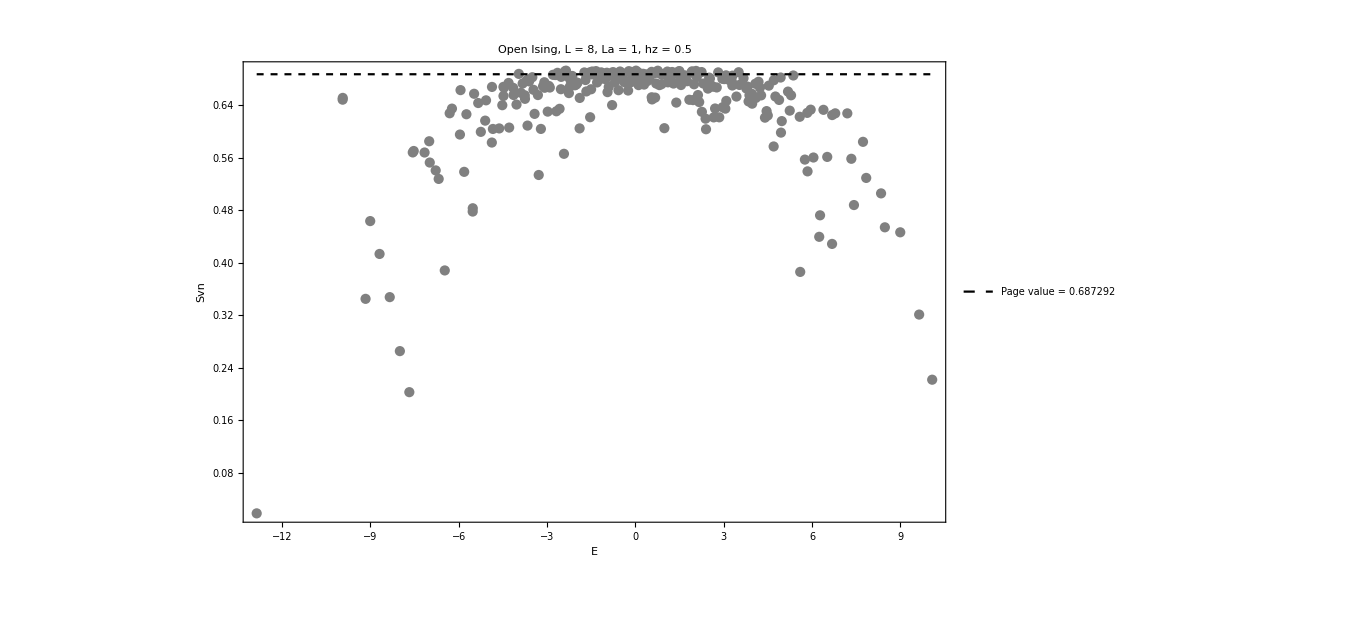

```mathematica
Show[{ListPlot[Transpose[{eigenval,sdiageigenvec}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Open Ising, L = "<>ToString[L]<>", La = "<>ToString[La]<>", hz = "<>ToString[hz],35,Black],PlotStyle->{Directive[Gray,Opacity[1]]},PlotRange->All,ImageSize->1000,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],Style["Svn"]}],Plot[pageEntropy[La,Lb],{x,Min[eigenval],Max[eigenval]},PlotStyle->{Directive[Black,Dashed]},PlotLegends->{Style["Page value = "<>ToString[N[pageEntropy[La,Lb]]],20,Black]}]},PlotRange->All]
```

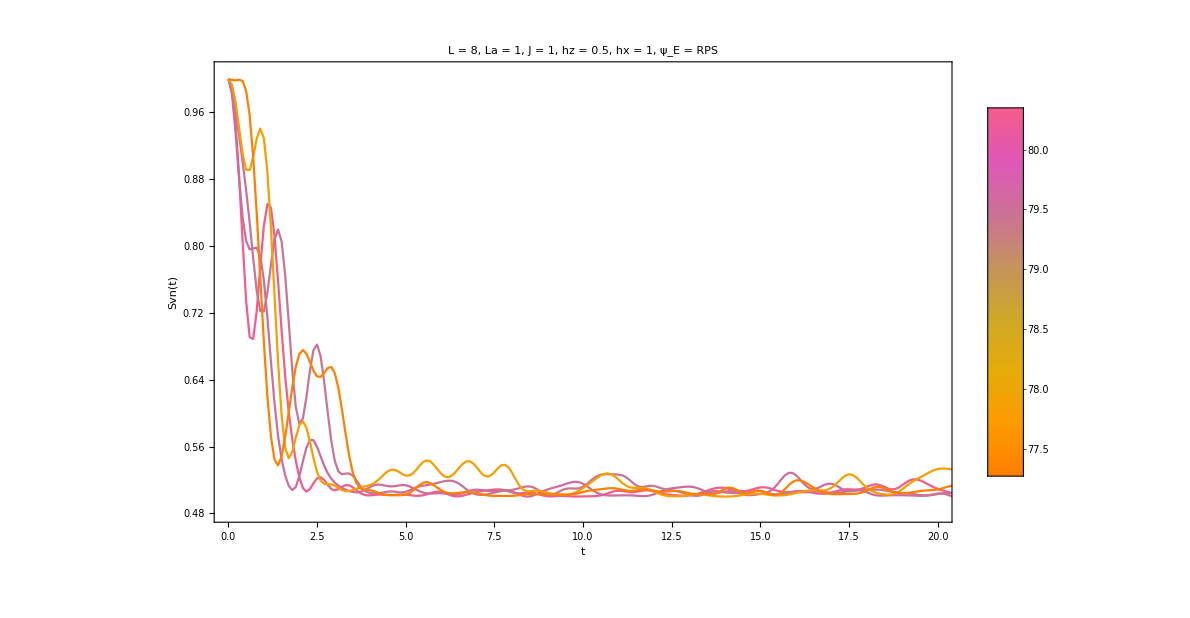

```mathematica
sorted=1/data[[All,1]];
{Emin,Emax}={Min[sorted],Max[sorted]};
colorMapping[e_]:=ColorData["FruitPunchColors"][Rescale[e,{Emin,Emax}]];
(*plot*)
plots=Table[ListPlot[svnt[[i]],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", hx = "<>ToString[hx]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->{{tlist[[1]],20},{0.48,1.01}},ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]]]],{i,Length[productstates]}];
Legended[Show[{plots}],BarLegend[{"FruitPunchColors",{Emin,Emax}},LabelStyle->{FontSize->12}]]
```

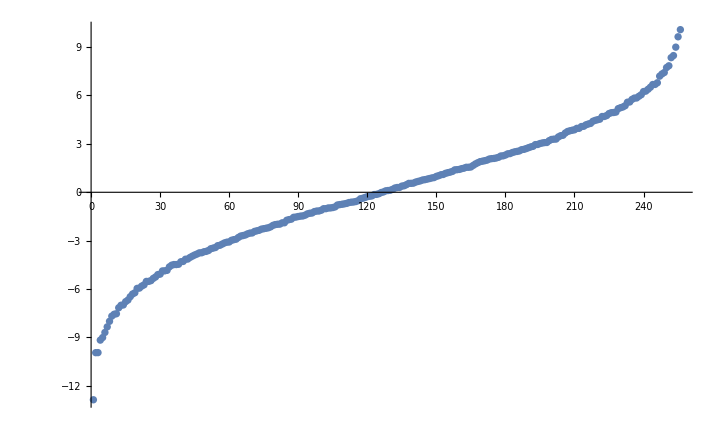

```mathematica
ListPlot[eigenval]
```

# Choi matrix ising

```mathematica
L=6;
hx=1;
J=1;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
dim=2^L;
```

```mathematica
(*FULL STATES*)
productstate2=Table[RandomChainProductState[L],2000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[eigenvec].i]^4]],{i,productstate2},DistributedContexts->Full];
data=SortBy[Transpose[{iprs,productstate2}],First];
data=Table[data[[i]],{i,1,2000,400}];
productstates=data[[All,2]];
```

```mathematica
(*EVEN PARITY STATES*)
allstates={};
Do[
a=Table[RandomQubitState[],L/2];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@a],Flatten[KroneckerProduct@@Reverse[a]]]];
AppendTo[allstates,evenini];
,{i,500}];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[eigenvec].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{iprs,allstates}],First];
data=Table[data[[i]],{i,1,500,100}];
productstates=data[[All,2]];
```

```mathematica
Min[1/iprs]
Max[1/iprs]
```

1.5071

27.5168

```mathematica
1/data[[All,1]]
```

{27.5168,18.6828,16.2326,13.6159,10.9342}

```mathematica
tlist=Table[i,{i,0,20,0.1}];
```

```mathematica
La=1;
Lb=L-La;
```

```mathematica
svnt=Table[ParallelTable[{t,svn[L,La,Lb,i,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full],{i,data[[All,2]]}];
```

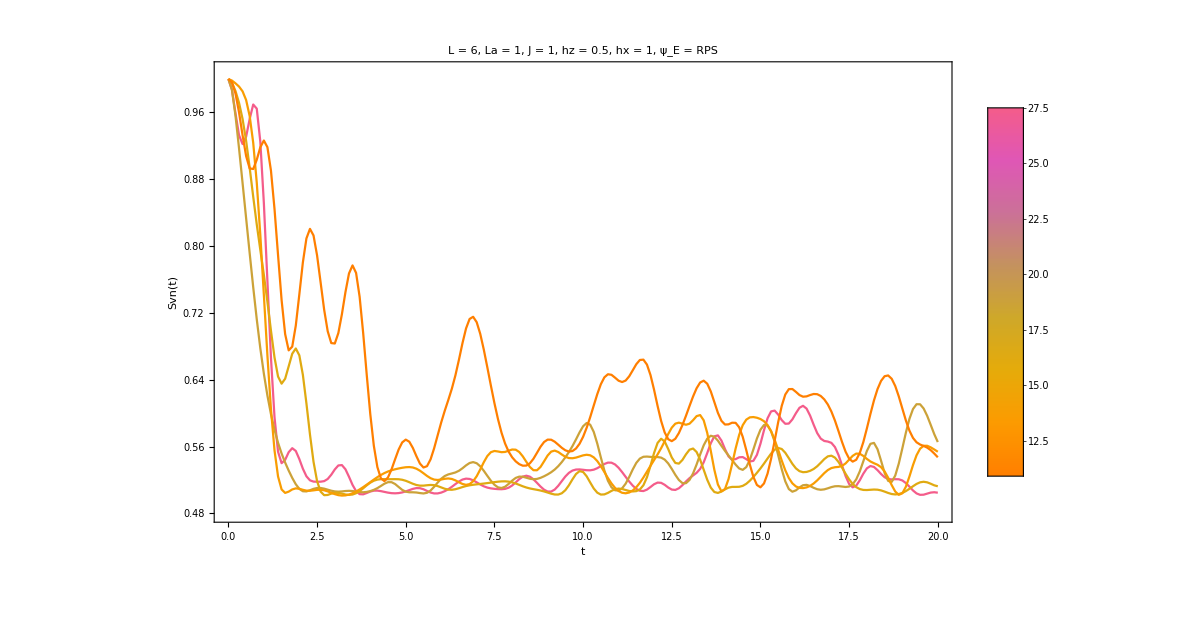

```mathematica
sorted=1/data[[All,1]];
{Emin,Emax}={Min[sorted],Max[sorted]};
colorMapping[e_]:=ColorData["FruitPunchColors"][Rescale[e,{Emin,Emax}]];
(*plot*)
plots=Table[ListPlot[svnt[[i]],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", hx = "<>ToString[hx]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->{{tlist[[1]],20},{0.48,1.01}},ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]]]],{i,Length[productstates]}];
Legended[Show[{plots}],BarLegend[{"FruitPunchColors",{Emin,Emax}},LabelStyle->{FontSize->12}]]
```

## RPS ψ_E

```mathematica
allplots={};
```

```mathematica
Do[

Lb=L-La;
ψ=productstates[[i]];
rho=MatrixPartialTrace[Dyad[ψ],1,{2^La,2^Lb}];
A=KroneckerProduct[IdentityMatrix[2^(Lb),SparseArray]/2^(La),rho];
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
P=Transpose[eigenvecs];
Pinv=Conjugate[eigenvecs];
ClearAll[U];
U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t]].Pinv;
chois=ParallelTable[ChoiMatrix[U[t],A,La,Lb],{t,tlist},DistributedContexts->Full];
purity=ParallelTable[Chop[Tr[i.i]],{i,Chop[chois]},DistributedContexts->Full];
plot=ListLogLinearPlot[Transpose[{tlist,purity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>",RPS ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]]],PlotLegends->{Style["RPS ψ_E, IPR = "<>ToString[sorted[[i]]],Opacity[1.0]]}];
final=Show[{plot,LogLinearPlot[(1/2^La)^2,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]],LogLinearPlot[0.5,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Purple,Dashed]]}];
(*Export["choi_RPS_"<>ToString[i]<>"_loglinear_purity_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_J_"<>ToString[J]<>"_hz_"<>ToString[hz]<>"_.png",final,ImageResolution->300]*);
AppendTo[allplots,final];
,{i,Length[productstates]}];
(*Export["choi_RPS_ALL_loglinear_purity_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_J_"<>ToString[J]<>"_hz_"<>ToString[hz]<>"_.gif",allplots,"DisplayDurations"->1.0,"AnimationRepetitions"->Infinity]*)
```

```mathematica
ListAnimate[allplots,AnimationRunning->False]
```

# Choi matrix Δ1

```mathematica
L=8;
hx=1;
J=1.5;
hz=0.75;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
dim=2^L;
```

```mathematica
(*FULL STATES*)
productstate2=Table[RandomChainProductState[L],2000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[eigenvec].i]^4]],{i,productstate2},DistributedContexts->Full];
data=SortBy[Transpose[{iprs,productstate2}],First];
data=Table[data[[i]],{i,1,2000,400}];
productstates=data[[All,2]];
```

```mathematica
(*EVEN PARITY STATES*)
allstates={};
Do[
a=Table[RandomQubitState[],L/2];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@a],Flatten[KroneckerProduct@@Reverse[a]]]];
AppendTo[allstates,evenini];
,{i,500}];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[eigenvec].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{iprs,allstates}],First];
data=Table[data[[i]],{i,1,500,100}];
productstates=data[[All,2]];
```

```mathematica
Min[1/iprs]
Max[1/iprs]
```

5.4316

79.222

```mathematica
1/data[[All,1]]
```

{79.222,53.0673,42.8469,34.5254,24.8998}

```mathematica
tlist=Table[i,{i,0,30,0.1}];
```

```mathematica
La=1;
Lb=L-La;
```

```mathematica
svnt=Table[ParallelTable[{t,svn[L,La,Lb,i,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full],{i,data[[All,2]]}];
```

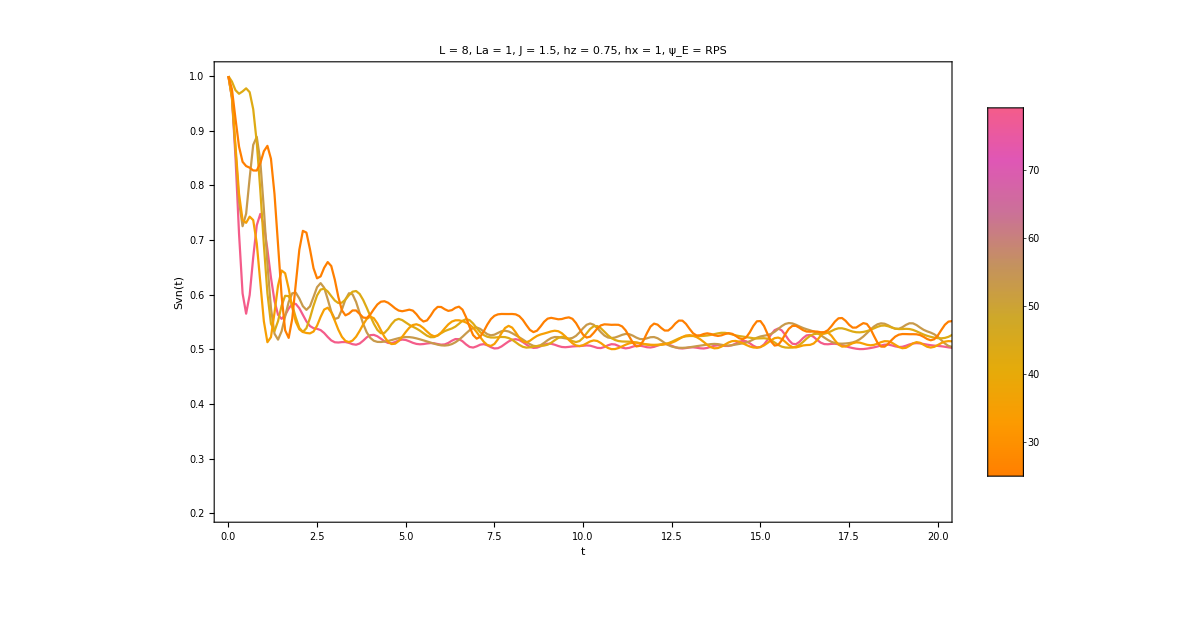

```mathematica
sorted=1/data[[All,1]];
{Emin,Emax}={Min[sorted],Max[sorted]};
colorMapping[e_]:=ColorData["FruitPunchColors"][Rescale[e,{Emin,Emax}]];
(*plot*)
plots=Table[ListPlot[svnt[[i]],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", hx = "<>ToString[hx]<>", ψ_E = RPS",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->{{tlist[[1]],20},{0.2,1.01}},ImageSize->1000,PlotStyle->Directive[colorMapping[sorted[[i]]]]],{i,Length[productstates]}];
Legended[Show[{plots}],BarLegend[{"FruitPunchColors",{Emin,Emax}},LabelStyle->{FontSize->12}]]
```

## RPS ψ_E

```mathematica
Lb=L-La;
i=5;
ψ=productstates[[i]];
rho=MatrixPartialTrace[Dyad[ψ],1,{2^La,2^Lb}];
A=KroneckerProduct[IdentityMatrix[2^(Lb),SparseArray]/2^(La),rho];
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
P=Transpose[eigenvecs];
Pinv=Conjugate[eigenvecs];
ClearAll[U];
U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t]].Pinv;
chois=ParallelTable[ChoiMatrix[U[t],A,La,Lb],{t,tlist},DistributedContexts->Full];
```

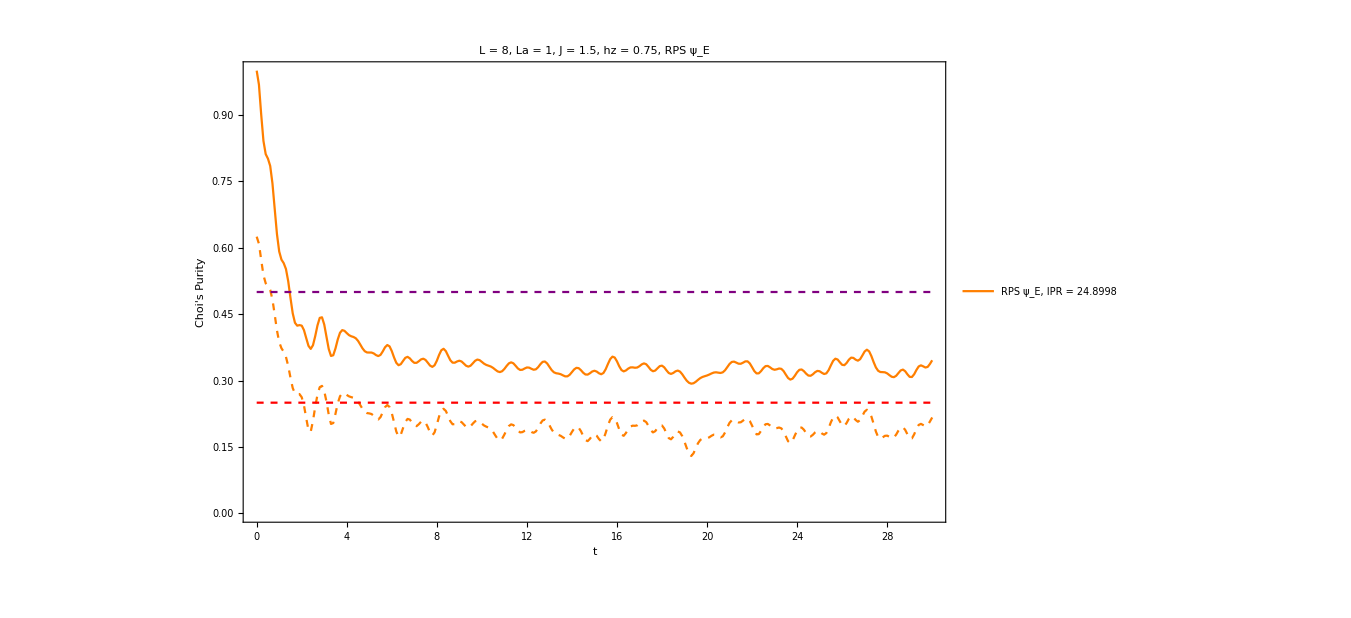

```mathematica
purity=ParallelTable[Chop[Tr[i.i]],{i,Chop[chois]},DistributedContexts->Full];
schmidts=ParallelTable[Sort[Chop[Eigenvalues[i]]],{i,Chop[chois]},DistributedContexts->Full];
delta=(1/2)Table[Sum[Abs[(i[[j]]^2)-1/8],{j,Length[i]}],{i,schmidts}];
plot=ListPlot[{Transpose[{tlist,purity}],Transpose[{tlist,delta}]},PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", RPS ψ_E",30,Black],Joined->{True,True},Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->{Directive[colorMapping[sorted[[i]]]],Directive[colorMapping[sorted[[i]]],Dashed]},PlotLegends->{Style["RPS ψ_E, IPR = "<>ToString[sorted[[i]]],Opacity[1.0]]}];
final=Show[{plot,Plot[(1/2^La)^2,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]],Plot[0.5,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Purple,Dashed]]}]
```

```mathematica
purity=ParallelTable[Chop[Tr[i.i]],{i,Chop[chois]},DistributedContexts->Full];
schmidts=ParallelTable[Sort[Chop[Eigenvalues[i]]],{i,Chop[chois]},DistributedContexts->Full];
delta=(1/2)Table[Sum[Abs[(i[[j]]^2)-1/8],{j,Length[i]}],{i,schmidts}];
plot=ListPlot[{Transpose[{tlist,purity}],Transpose[{tlist,delta}]},PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", RPS ψ_E",30,Black],Joined->{True,True},Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->{Directive[colorMapping[sorted[[i]]]],Directive[colorMapping[sorted[[i]]],Dashed]},PlotLegends->{Style["RPS ψ_E, IPR = "<>ToString[sorted[[i]]],Opacity[1.0]]}];
final=Show[{plot,Plot[(1/2^La)^2,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]],Plot[0.5,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Purple,Dashed]]}]
```

-Graphics-

```mathematica
purity=ParallelTable[Chop[Tr[i.i]],{i,Chop[chois]},DistributedContexts->Full];
schmidts=ParallelTable[Sort[Chop[Eigenvalues[i]]],{i,Chop[chois]},DistributedContexts->Full];
delta=(1/2)Table[Sum[Abs[(i[[j]]^2)-1/8],{j,Length[i]}],{i,schmidts}];
plot=ListPlot[{Transpose[{tlist,purity}],Transpose[{tlist,delta}]},PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", RPS ψ_E",30,Black],Joined->{True,True},Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->{Directive[colorMapping[sorted[[i]]]],Directive[colorMapping[sorted[[i]]],Dashed]},PlotLegends->{Style["RPS ψ_E, IPR = "<>ToString[sorted[[i]]],Opacity[1.0]]}];
final=Show[{plot,Plot[(1/2^La)^2,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]],Plot[0.5,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Purple,Dashed]]}]
```

-Graphics-

```mathematica
purity=ParallelTable[Chop[Tr[i.i]],{i,Chop[chois]},DistributedContexts->Full];
schmidts=ParallelTable[Sort[Chop[Eigenvalues[i]]],{i,Chop[chois]},DistributedContexts->Full];
delta=(1/2)Table[Sum[Abs[(i[[j]]^2)-1/8],{j,Length[i]}],{i,schmidts}];
plot=ListPlot[{Transpose[{tlist,purity}],Transpose[{tlist,delta}]},PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", RPS ψ_E",30,Black],Joined->{True,True},Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->{Directive[colorMapping[sorted[[i]]]],Directive[colorMapping[sorted[[i]]],Dashed]},PlotLegends->{Style["RPS ψ_E, IPR = "<>ToString[sorted[[i]]],Opacity[1.0]]}];
final=Show[{plot,Plot[(1/2^La)^2,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]],Plot[0.5,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Purple,Dashed]]}]
```

-Graphics-

```mathematica
purity=ParallelTable[Chop[Tr[i.i]],{i,Chop[chois]},DistributedContexts->Full];
schmidts=ParallelTable[Sort[Chop[Eigenvalues[i]]],{i,Chop[chois]},DistributedContexts->Full];
delta=(1/2)Table[Sum[Abs[(i[[j]]^2)-1/8],{j,Length[i]}],{i,schmidts}];
plot=ListPlot[{Transpose[{tlist,purity}],Transpose[{tlist,delta}]},PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", RPS ψ_E",30,Black],Joined->{True,True},Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->{Directive[colorMapping[sorted[[i]]]],Directive[colorMapping[sorted[[i]]],Dashed]},PlotLegends->{Style["RPS ψ_E, IPR = "<>ToString[sorted[[i]]],Opacity[1.0]]}];
final=Show[{plot,Plot[(1/2^La)^2,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]],Plot[0.5,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Purple,Dashed]]}]
```

-Graphics-

```mathematica
AssociationThread
```